```mathematica
Clear[forcex,forcey,forcexMag,forceyMag,dog,pendulumForcex,pendulumForcey,PositionPend,PositionPendCube,eForcex,eForcey,dampingx,dampingy,eForcex2,eForcey2]
```

```mathematica
forcesx = m x''[t];
forcesy = m y''[t];
pendulumForcex = -(m*x[t])*((1-((x[t]^2+y[t]^2))/(L^2))^(1/2))*(g/L);
pendulumForcey = -(m*y[t])*((1-((x[t]^2+y[t]^2))/(L^2))^(1/2))*(g/L);
dog = (L(1-Sqrt[1-((x[t])^2+y[t]^2)/L^2]));
dog2 = (L(1-Sqrt[1-((x[t])^2+y[t]^2)/L^2]));;
PositionPendCube1 = (((x[t]+1.0)^2)+((y[t]+0.0)^2)+((dog+d)^2))^(3/2);
PositionPendCube2 = (((x[t]-1.0)^2)+((y[t]-0.0)^2)+((dog+d)^2))^(3/2);
eForcex = (-k*(x[t]+1.0))/PositionPendCube1;
eForcey = (-k*y[t])/PositionPendCube1;
eForcex2 = (-k*(x[t]-1.0))/PositionPendCube2;
eForcey2 = (-k*y[t])/PositionPendCube2;
dampingx = -c*x'[t];
dampingy = -c*y'[t];
```

```mathematica
equationPendx ={ forcesx == eForcex+eForcex2+pendulumForcex+ dampingx};
equationPendy ={ forcesy == eForcey+eForcey2+pendulumForcey+ dampingy};
```

```mathematica
equationPendx =Expand[{ forcesx/m == (eForcex+eForcex2+pendulumForcex + dampingx)/m}]/.{g/L ->Subscript[ω, 0]^2, k/m ->Subscript[ω, 1]^2, c/m -> 2ζ}
equationPendy =Expand[{ forcesy/m == (eForcey+eForcey2+pendulumForcey + dampingy)/m}]/.{g/L ->Subscript[ω, 0]^2, k/m ->Subscript[ω, 1]^2, c/m -> 2ζ}
```

{x''[t]==-ω_0^2 x[t] √(1-(x[t]^2+y[t]^2)/L^2)+(1. ω_1^2)/(((-1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(ω_1^2 x[t])/(((-1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(1. ω_1^2)/(((1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(ω_1^2 x[t])/(((1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-2 ζ x'[t]}

{y''[t]==-ω_0^2 y[t] √(1-(x[t]^2+y[t]^2)/L^2)-(ω_1^2 y[t])/(((-1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(ω_1^2 y[t])/(((1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-2 ζ y'[t]}

```mathematica
initConditionsPendx= {x[0] == x0, x'[0] ==vx0}
initConditionsPendy= {y[0] == y0, y'[0] ==vy0}
```

{x[0]==x0,x'[0]==vx0}

{y[0]==y0,y'[0]==vy0}

```mathematica
eqAndICPend = Join[equationPendx ,initConditionsPendx,equationPendy ,initConditionsPendy]
{Subscript[ω, 0]->1,Subscript[ω, 1]->1,ζ->0.1, L -> 10.,d->0.2}
eqAndICPendN[x0_,y0_,vx0_,vy0_] = eqAndICPend/.{Subscript[ω, 0]->1,Subscript[ω, 1]->1,ζ->0.1, L -> 10.,d->0.2}
```

{x''[t]==-ω_0^2 x[t] √(1-(x[t]^2+y[t]^2)/L^2)+(1. ω_1^2)/(((-1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(ω_1^2 x[t])/(((-1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(1. ω_1^2)/(((1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(ω_1^2 x[t])/(((1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-2 ζ x'[t],x[0]==x0,x'[0]==vx0,y''[t]==-ω_0^2 y[t] √(1-(x[t]^2+y[t]^2)/L^2)-(ω_1^2 y[t])/(((-1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-(ω_1^2 y[t])/(((1.+x[t])^2+y[t]^2+(d+L √(((1+x[t])^2+y[t]^2)/L^2))^2)^(3/2))-2 ζ y'[t],y[0]==y0,y'[0]==vy0}

{ω_0→1,ω_1→1,ζ→0.1,L→10.,d→0.2}

{x''[t]==-x[t] √(1-0.01 (x[t]^2+y[t]^2))+1./(((-1.+x[t])^2+y[t]^2+(0.2+1. √((1+x[t])^2+y[t]^2))^2)^(3/2))-x[t]/(((-1.+x[t])^2+y[t]^2+(0.2+1. √((1+x[t])^2+y[t]^2))^2)^(3/2))-1./(((1.+x[t])^2+y[t]^2+(0.2+1. √((1+x[t])^2+y[t]^2))^2)^(3/2))-x[t]/(((1.+x[t])^2+y[t]^2+(0.2+1. √((1+x[t])^2+y[t]^2))^2)^(3/2))-0.2 x'[t],x[0]==x0,x'[0]==vx0,y''[t]==-y[t] √(1-0.01 (x[t]^2+y[t]^2))-y[t]/(((-1.+x[t])^2+y[t]^2+(0.2+1. √((1+x[t])^2+y[t]^2))^2)^(3/2))-y[t]/(((1.+x[t])^2+y[t]^2+(0.2+1. √((1+x[t])^2+y[t]^2))^2)^(3/2))-0.2 y'[t],y[0]==y0,y'[0]==vy0}

```mathematica
solPend = NDSolve[eqAndICPendN[1,1,1,-1],{x,y},{t,0,50}]
```

{{x→InterpolatingFunction[{{0., 50.}}, <>],y→InterpolatingFunction[{{0., 50.}}, <>]}}

```mathematica
xPend[t_]=First[ x[t]/.solPend]
yPend[t_]=First[ y[t]/.solPend]
```

InterpolatingFunction[{{0., 50.}}, <>][t]

InterpolatingFunction[{{0., 50.}}, <>][t]

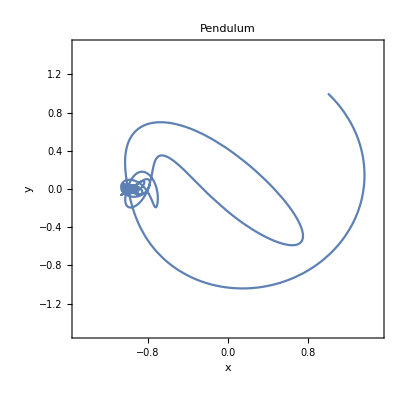

```mathematica
ParametricPlot[
				{
					xPend[t],
					yPend[t]
				},
				{t,0,50},
				PlotRange->{{-1.5,1.5},{-1.5,1.5}},
				Frame->True,
				FrameLabel->{Style["x",14],Style["y",14]},
				PlotLabel-> Style["Pendulum",18],
				Axes -> False
]
```

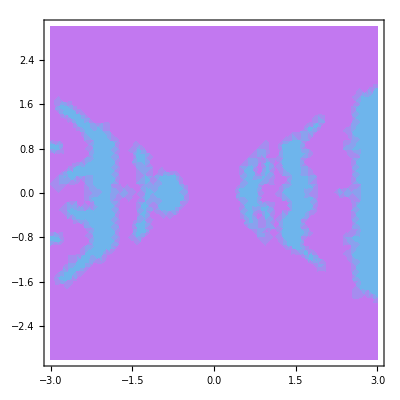

```mathematica
Clear[PendMap,PendMap2,color]
PendMap[x0_,y0_]:= Module[
{},solPendMap = NDSolve[eqAndICPendN[x0,y0,0,0],{x,y},{t,0,25}];

xPendMap[t_]=First[ x[t]/.solPendMap];
yPendMap[t_]=First[ y[t]/.solPendMap];

color := 0;
color := 1/;(Norm[{xPendMap[25],yPendMap[25]}-{1,0}] < 0.3);
color := 2/;(Norm[{xPendMap[25],yPendMap[25]}-{-1,0}]<0.3);
Return[color];

];

dp1 = DensityPlot[
				PendMap[x0,y0],
				{x0,-3,3},
				{y0,-3,3},
				PlotPoints->20,
				PlotRange->{Full,Full,Full},
				ColorFunction->"Pastel"
	]
```